```mathematica
m=Transpose[{{1-fm*fp,0,0,0,fm*fp},{0,(1-fm)(1-fp),fm(1-fp),fp(1-fm),fm*fp},{fp,(1-fm)(1-fp),fm(1-fp),0,0},{fm,(1-fm)(1-fp),0,fp(1-fm),0},{1-(1-fm)(1-fp),(1-fm)(1-fp),0,0,0}}]; (*fm is the presynaptic sparsity, fp is the postsynaptic sparsity*)
```

```mathematica
MatrixForm[m]
```

(1-fm fp | 0 | fp | fm | 1-(1-fm) (1-fp)
0 | (1-fm) (1-fp) | (1-fm) (1-fp) | (1-fm) (1-fp) | (1-fm) (1-fp)
0 | fm (1-fp) | fm (1-fp) | 0 | 0
0 | (1-fm) fp | 0 | (1-fm) fp | 0
fm fp | fm fp | 0 | 0 | 0)

```mathematica
Total[m] //Simplify
```

{1,1,1,1,1}

```mathematica
evals=Eigenvalues[m]
```

{1,Root[-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4+(fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) #1+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4&,1],Root[-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4+(fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) #1+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4&,2],Root[-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4+(fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) #1+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4&,3],Root[-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4+(fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) #1+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4&,4]}

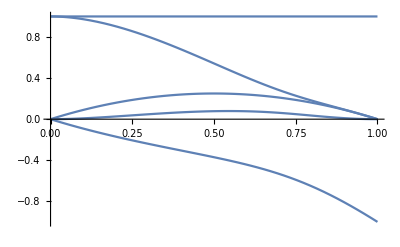

```mathematica
Plot[evals/.fp-> f /.fm->f,{f,0,1}]
```

```mathematica
evals /.fm->.01 /. fp->.01
```

{1,-0.00990194,0.0000980198,0.0099,0.999704}

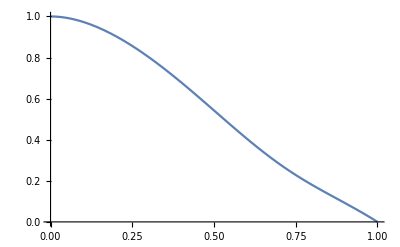

```mathematica
λ2=evals[[5]];
Plot[λ2/.fp->f/.fm->f,{f,0,1}]
```

```mathematica
Series[λ2,{fp,0,2}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4+(fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) #1+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4& for some values of {fm,fp}.

1+(-3 fm+2 fm^2) fp+(2 fm-8 fm^2+11 fm^3-5 fm^4) fp^2+O[fp]^3

```mathematica
evl=Eigenvectors[Transpose[m]];
```

```mathematica
evr=Eigenvectors[m];
evl1=evl[[1]];
evl2=evl[[5]];
evr1=evr[[1]];
evr2=evr[[5]];
evr1=evr1/Total[evr1*evl1];
evr2=evr2/Total[evr2*evl2];
evr1 //Simplify
```

{(-2+fp+fm^3 (-1+fp)^2 fp+fm^2 fp (-3+5 fp-2 fp^2)+fm (1+fp-3 fp^2+fp^3))/(-3+2 fp-2 fm^2 (-1+fp)^2 fp+fm^3 (-1+fp)^2 fp+fm (2-2 fp-2 fp^2+fp^3)),-((-1+fm) (1+fm (-1+fp)) (-1+fp) (1+(-1+fm) fp))/(-3+2 fp-2 fm^2 (-1+fp)^2 fp+fm^3 (-1+fp)^2 fp+fm (2-2 fp-2 fp^2+fp^3)),((-1+fm) fm (-1+fp)^2 (1+(-1+fm) fp))/(-3+2 fp-2 fm^2 (-1+fp)^2 fp+fm^3 (-1+fp)^2 fp+fm (2-2 fp-2 fp^2+fp^3)),((-1+fm)^2 (1+fm (-1+fp)) (-1+fp) fp)/(-3+2 fp-2 fm^2 (-1+fp)^2 fp+fm^3 (-1+fp)^2 fp+fm (2-2 fp-2 fp^2+fp^3)),-(fm fp (3+fm^2 (-1+fp)^2-3 fp+fp^2+fm (-3+5 fp-2 fp^2)))/(-3+2 fp-2 fm^2 (-1+fp)^2 fp+fm^3 (-1+fp)^2 fp+fm (2-2 fp-2 fp^2+fp^3))}

```mathematica
w=1-evr1[[1]]
```

1+(-2+fm+fp+fm fp-3 fm^2 fp+fm^3 fp-3 fm fp^2+5 fm^2 fp^2-2 fm^3 fp^2+fm fp^3-2 fm^2 fp^3+fm^3 fp^3)/(fm fp (3-3 fm+fm^2-3 fp+5 fm fp-2 fm^2 fp+fp^2-2 fm fp^2+fm^2 fp^2) (1+((-1+fm) (1-fp+fm fp) (-1+fm+fp-2 fm fp+fm fp^2))/(fm fp (3-3 fm+fm^2-3 fp+5 fm fp-2 fm^2 fp+fp^2-2 fm fp^2+fm^2 fp^2))-(-1+3 fm-3 fm^2+fm^3+fp-4 fm fp+5 fm^2 fp-2 fm^3 fp+fm fp^2-2 fm^2 fp^2+fm^3 fp^2)/(fm (3-3 fm+fm^2-3 fp+5 fm fp-2 fm^2 fp+fp^2-2 fm fp^2+fm^2 fp^2))-((-1+fm) (1-3 fp+fm fp+3 fp^2-2 fm fp^2-fp^3+fm fp^3))/(fp (3-3 fm+fm^2-3 fp+5 fm fp-2 fm^2 fp+fp^2-2 fm fp^2+fm^2 fp^2))-(-2+fm+fp+fm fp-3 fm^2 fp+fm^3 fp-3 fm fp^2+5 fm^2 fp^2-2 fm^3 fp^2+fm fp^3-2 fm^2 fp^3+fm^3 fp^3)/(fm fp (3-3 fm+fm^2-3 fp+5 fm fp-2 fm^2 fp+fp^2-2 fm fp^2+fm^2 fp^2))))

```mathematica
x0={evr1[[3]]+evr1[[4]]+evr1[[5]],0,0,0,evr1[[1]]+evr1[[2]]};
```

```mathematica
(*MatrixForm[Sum[evals[[k]]*TensorProduct[evr[[k]],evl[[k]]],{k,1,5}]]//Simplify*)
pw0=1-x0[[1]];
```

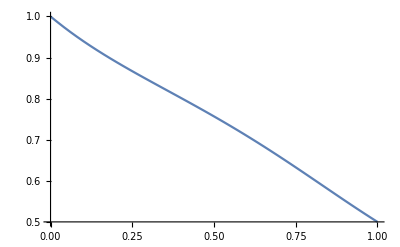

```mathematica
Plot[pw0 /. fp->f /.fm->f,{f,0,1}]
```

```mathematica
pw0 /. fm->f /. fp->f //Simplify
```

-(3-3 f+f^2)/(-3+f+2 f^2-3 f^3+f^4)

```mathematica
(pw0-w)/(pw0(1-pw0)+w(1-w)) /.fm->f /.fp->f //Simplify
```

-((-1+f) (-3+f+2 f^2-3 f^3+f^4))/(-1-2 f+8 f^2-13 f^3+11 f^4-5 f^5+f^6)

```mathematica
snr0=(pw0-w)/(pw0(1-pw0)+w(1-w));
```

```mathematica
λ2  /. fp->f /.fm->f //ToRadicals //Simplify
```

-(-1+f) f

```mathematica
λ2 //ToRadicals
```

1/4 (1-2 fm fp)+1/2 √(fm^2 fp+fm fp^2-2 fm^2 fp^2+1/4 (-1+2 fm fp)^2+1/3 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+(2^(1/3) (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4))/(3 (27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)+√(-4 (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4)^3+(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4))^2))^(1/3))+1/(3 2^(1/3))(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)+√(-4 (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4)^3+(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4))^2))^(1/3))+1/2 √(fm^2 fp+fm fp^2-2 fm^2 fp^2+1/2 (-1+2 fm fp)^2+1/3 (fm^2 fp+fm fp^2-2 fm^2 fp^2)-(2^(1/3) (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4))/(3 (27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)+√(-4 (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4)^3+(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4))^2))^(1/3))-1/(3 2^(1/3))(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)+√(-4 (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4)^3+(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4))^2))^(1/3)+(-(-1+2 fm fp)^3-8 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)+4 (-1+2 fm fp) (-fm^2 fp-fm fp^2+2 fm^2 fp^2))/(4 √(fm^2 fp+fm fp^2-2 fm^2 fp^2+1/4 (-1+2 fm fp)^2+1/3 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+(2^(1/3) (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4))/(3 (27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)+√(-4 (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4)^3+(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4))^2))^(1/3))+1/(3 2^(1/3))(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)+√(-4 (3 fm fp-3 fm^2 fp-3 fm fp^2-15 fm^2 fp^2+30 fm^3 fp^2-11 fm^4 fp^2+30 fm^2 fp^3-52 fm^3 fp^3+20 fm^4 fp^3-11 fm^2 fp^4+20 fm^3 fp^4-8 fm^4 fp^4)^3+(27 (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2)^2-9 (-1+2 fm fp) (fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) (-fm^2 fp-fm fp^2+2 fm^2 fp^2)+2 (-fm^2 fp-fm fp^2+2 fm^2 fp^2)^3+27 (-1+2 fm fp)^2 (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4)-72 (-fm^2 fp-fm fp^2+2 fm^2 fp^2) (-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4))^2))^(1/3))))

```mathematica
Series[λ2,{fp,0,2}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+2 fm^2 fp^3-4 fm^3 fp^3+2 fm^4 fp^3-fm^2 fp^4+2 fm^3 fp^4-fm^4 fp^4+(fm fp-fm^2 fp-fm fp^2+fm^2 fp^2) #1+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4& for some values of {fm,fp}.

1+(-3 fm+2 fm^2) fp+(2 fm-8 fm^2+11 fm^3-5 fm^4) fp^2+O[fp]^3

```mathematica
x0={evr1[[3]]+evr1[[4]]+evr1[[5]],0,0,0,evr1[[1]]+evr1[[2]]};
snr=((np*nm*fp*fm)λ2^(2t)(1-evr2[[1]]*evl2.x0)/(2w(1-w)))^(1/2);
```

```mathematica
thr=1/(6fm*fp)Log[Nm*Np*fm*fp*Log[Np*Nm]/(2w(1-w))];
```

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["BTSP_uncorr_N1000_10logN.mat"];
```

```mathematica
tdata=data[[5]][[1]];
```

```mathematica
snrdata=data[[4]][[1]];
sigdata=data[[1]][[1]];
vardata=data[[2]][[1]];
varranddata=data[[3]][[1]];
```

```mathematica
dt=ListPlot[Transpose[{tdata,snrdata}]];
```

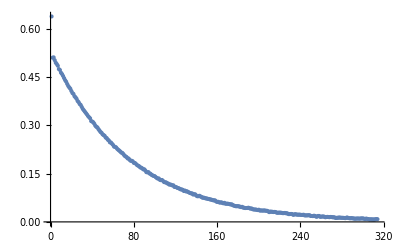

```mathematica
sigdatapl=ListPlot[Transpose[{tdata,sigdata}]]
```

```mathematica
sigp=λ2^(t)*(1-evr2[[1]]*evl2.x0)
```

Root[-fm^2 fp^2+2 fm^3 fp^2-fm^4 fp^2+10+(-fm^2 fp-fm fp^2+2 fm^2 fp^2) #1^2+(-1+2 fm fp) #1^3+#1^4&,4]^t (1+((-fm^2 fp+19+fm fp Root[1&,4]^2) (1/1-1+1/1))/((-fm fp+fm^3 fp+21+3 fm fp Root[1]^2+Root[1&,4]^3) (6+1)))
 |  |  |  |

```mathematica
sigp2=1-Sum[evals[[k]]^t*evl[[k]].x0*evr[[1]],{k,2,5}]
```

{1}
 |  |  |  |

```mathematica
xt=Sum[evals[[k]]^t(evl[[k]].x0)/(evl[[k]].evr[[k]])*evr[[k]],{k,1,5}];
```

```mathematica
sigt=1-Sum[evals[[k]]^t(evl[[k]].x0)/(evl[[k]].evr[[k]])*evr[[k]][[1]],{k,2,5}];
```

```mathematica
evl2.evr2 //Simplify
```

1

```mathematica
m2=Sum[evals[[k]]*TensorProduct[evr[[k]],evl[[k]]]/(evl[[k]].evr[[k]]),{k,1,5}];
```

```mathematica
MatrixForm[m2] /.fp->.07 /.fm->.07
```

(0.9951 | 1.11022×10^-14 | 0.060886 | 0.079114 | 0.1351
2.38698×10^-15 | 0.8649 | 0.8649 | 0.8649 | 0.8649
2.18575×10^-16 | 0.0651 | 0.09765 | -0.03255 | -5.48173×10^-16
2.74086×10^-16 | 0.0651 | 0.03255 | 0.03255 | -6.245×10^-16
0.0049 | 0.0049 | 0.004557 | -0.004557 | 5.61617×10^-17)

```mathematica
MatrixForm[m] /.fp->.07/.fm->.07
```

(0.9951 | 0 | 0.07 | 0.07 | 0.1351
0 | 0.8649 | 0.8649 | 0.8649 | 0.8649
0 | 0.0651 | 0.0651 | 0 | 0
0 | 0.0651 | 0 | 0.0651 | 0
0.0049 | 0.0049 | 0 | 0 | 0)

```mathematica
m2num=m/.fp->.07 /. fm->.07 //Chop
```

{{0.9951,0,0.07,0.07,0.1351},{0,0.8649,0.8649,0.8649,0.8649},{0,0.0651,0.0651,0,0},{0,0.0651,0,0.0651,0},{0.0049,0.0049,0,0,0}}

```mathematica
m2numt=MatrixPower[m2num,t] ;
```

```mathematica
xtnum2=m2numt.(x0/.fp->.07 /.fm->.07);
```

```mathematica
x0num=x0/.fp->.07 /.fm->.07;
```

```mathematica
diffvec=xtnum2-(evr1/. fp->.07 /.fm->.07);
```

```mathematica
signum=1-diffvec[[1]];
```

```mathematica
signum2=1-xtnum2[[1]];
```

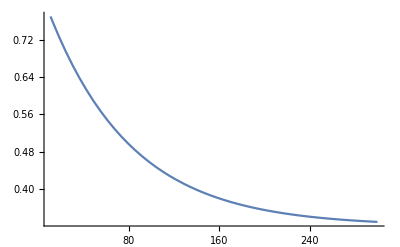

```mathematica
signum2pl=Plot[signum2,{t,0,300},PlotRange->All]
```

```mathematica
evrnum=evr1/. fp->.07 /.fm->.07
```

{0.679961,0.276802,0.0192746,0.0192746,0.00468814}

```mathematica
evrnum[[1]]-xtnum2[[1]] /.t->1
```

0.507677

```mathematica
signumtable=Table[evrnum[[1]]-xtnum2[[1]],{t,0,300}];
```

```mathematica
signumlp=ListPlot[signumtable,PlotStyle->Black];
```

```mathematica
m2approx=Sum[evals[[k]]*TensorProduct[evr[[k]],evl[[k]]]/(evl[[k]].evr[[k]]),{k,{1,5}}];
```

```mathematica
m2approxnum=m2approx /.fp->.07 /. fm->.07 //Chop;
```

```mathematica
MatrixForm[m2approxnum]
```

(0.995135 | 0.000573863 | 0.066185 | 0.066185 | 0.127487
0.000480214 | 0.872438 | 0.814915 | 0.814915 | 0.761171
-0.000248248 | 0.0613578 | 0.0572937 | 0.0572937 | 0.0534965
-0.000248248 | 0.0613578 | 0.0572937 | 0.0572937 | 0.0534965
0.00488112 | 0.00427215 | 0.00431232 | 0.00431232 | 0.00434986)

```mathematica
Total[m2approxnum]
```

{1.,1.,1.,1.,1.}

```mathematica
m2approxnumt=MatrixPower[m2approxnum,t];
```

```mathematica
xtnum2approx=m2approxnumt.x0num;
```

```mathematica
sigapprox=evrnum[[1]] - xtnum2approx[[1]];
```

```mathematica
sigapproxtable=Table[sigapprox,{t,10,300}];
```

```mathematica
sigapproxpl=ListPlot[sigapproxtable,PlotStyle->Red];
```

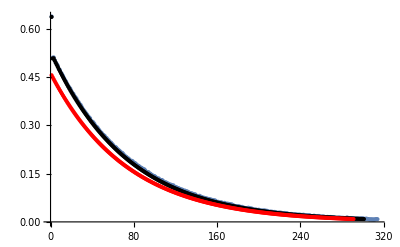

```mathematica
Show[sigdatapl,signumlp,sigapproxpl]
```

```mathematica
pwapprox=1 - xtnum2approx[[1]];
```

```mathematica
pwnum=1-xtnum2[[1]];
```

```mathematica
wnum=w/.fm->.07/.fp->.07
```

0.320039

```mathematica
pwnum /.t->1
```

0.827716

```mathematica
snrnum=((pwnum-wnum)^2/(pwnum(1-(.07^2)pwnum)+wnum(1-(.07^2)wnum)))^(1/2);
```

```mathematica
snrnumpl=ListPlot[Table[10Log[1000]*snrnum,{t,1,300}],PlotStyle->Black];
```

```mathematica
snrapprox=((pwapprox-wnum)^2/(pwapprox(1-(.07^2)pwapprox)+wnum(1-(.07^2)wnum)))^(1/2);
```

```mathematica
snrapproxpl=ListPlot[Table[10Log[1000]*snrapprox,{t,1,300}],PlotStyle->Red];
```

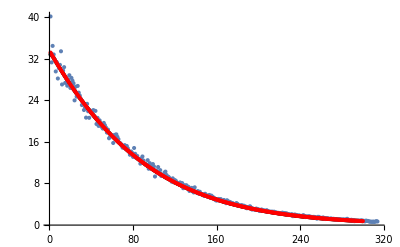

```mathematica
Show[snrnumpl,dt,snrapproxpl,PlotRange->All]
```

```mathematica
Export["./snrdata_btsp_uncorr_N1000_10logN_10logN.csv",snrdata]
```

./snrdata_btsp_uncorr_N1000_10logN_10logN.csv

```mathematica
snrnumexport=Table[10Log[1000]*snrnum,{t,0,300}];
```

```mathematica
Export["./snr_btsp_uncorr_N1000_10logN_10logN.csv",snrnumexport];

snrapproxexport=Table[10Log[1000]*snrapprox,{t,0,300}];
Export["./snrapprox_btsp_uncorr_N1000_10logN_10logN.csv",snrapproxexport];
```

```mathematica
xtnum2approx/.t->1
vardatapl=ListPlot[Transpose[{tdata,vardata}]]
```

{0.165001,0.72828,0.0511727,0.0511727,0.00437283}

```mathematica
varnum=pwnum(1-(.07^2)pwnum);
```

```mathematica
varnumpl=Plot[varnum/(10Log[1000])^2,{t,1,300}];
```

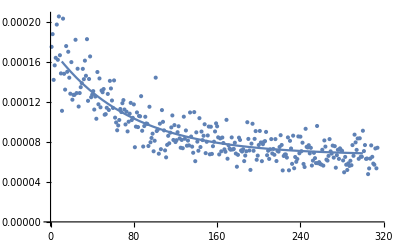

```mathematica
Show[vardatapl,varnumpl]
```

```mathematica
ppre=fm*(m /. fm->1);
```

```mathematica
MatrixForm[ppre]
```

(fm (1-fp) | 0 | fm fp | fm | fm
0 | 0 | 0 | 0 | 0
0 | fm (1-fp) | fm (1-fp) | 0 | 0
0 | 0 | 0 | 0 | 0
fm fp | fm fp | 0 | 0 | 0)

```mathematica
ppost=fp*(m/.fp->1);
```

```mathematica
MatrixForm[ppost]
```

((1-fm) fp | 0 | fp | fm fp | fp
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | (1-fm) fp | 0 | (1-fm) fp | 0
fm fp | fm fp | 0 | 0 | 0)

```mathematica
cop=(m/.fp->1)*fp;
```

```mathematica
copnum= cop/.fp->.07 /. fm->.07;
```

```mathematica
xc[tpre_,tpost_]:=(copnum /.t1->tpre /.t2->tpost).evrnum;
```

SetDelayed::write: Tag List in {0.0460373,0.,0.,0.0192746,0.00468814}[tpre_,tpost_] is Protected.

```mathematica
MatrixForm[ppre.ppost/(fp*fm)] //Simplify
```

(1+(-1+fm) fp | 1 | 1-fp | 1-fm fp | 1-fp
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
fp-fm fp | 0 | fp | fm fp | fp)

```mathematica
comp=ppre.MatrixPower[m,tpre-tpost-1].ppost.MatrixPower[m,tpost ].evr1;
```

```mathematica
copm=ppost.MatrixPower[m,tpost-tpre-1].ppre.MatrixPower[m,tpre ].evr1;
```

```mathematica
psim=fp*fm*(m/.fm->1 /.fp->1);
```

```mathematica
cos=psim*MatrixPower[m,tpost].evr1;
```

```mathematica
(*MatrixForm[comp  /.tpre->1 /.tpost->0] //Simplify*)
```

```mathematica
(*MatrixForm[ppre.MatrixPower[m,0].ppost.MatrixPower[m,0].evr1] //Simplify*)
```

```mathematica
compnum=MatrixPower[m/.fm->.07 /.fp->.07,tpost].(ppost /.fm->.07/.fp->.07).MatrixPower[m/.fm->.07/.fp->.07,tpre-tpost-1 ].(ppre /.fm->.07 /.fp->.07).(evr1/.fm->.07 /.fp->.07);
```

```mathematica
copmnum=MatrixPower[m/.fm->.07 /.fp->.07,tpre].(ppre /.fm->.07/.fp->.07).MatrixPower[m/.fm->.07/.fp->.07,tpost-tpre-1 ].(ppost /.fm->.07 /.fp->.07).(evr1/.fm->.07 /.fp->.07);
```

```mathematica
cosnum=MatrixPower[m/.fm->.07/.fp->.07,tpost].(psim/.fm->.07/.fp->.07).(evr1/.fp->.07/.fm->.07);
```

```mathematica
cowtest[t1_,t2_]=Which[t1==t2,1-(cosnum/.07^2/.tpre->t1 /.tpost->t2)[[1]] ,t1<t2,1-(copmnum/.07^2/.tpre->t1 /.tpost->t2)[[1]],t1>t2,1-(compnum/.07^2 /.tpre->t1/.tpost->t2)[[1]]];
```

```mathematica
pwc=Table[cowtest[t1,t2],{t1,0,150},{t2,0,150}];
```

General::munfl: 0.0000185631 3.52844×10^-304 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

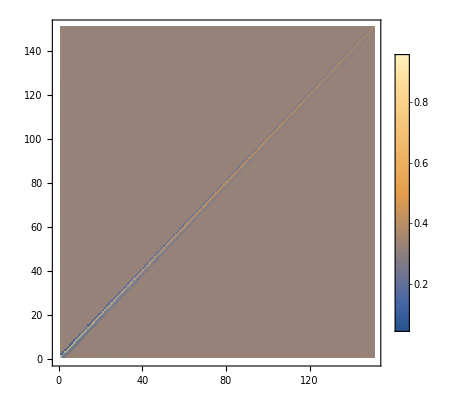

```mathematica
ListDensityPlot[pwc,PlotLegends->Automatic,PlotRange->{0,1}]
```